# Decision boundary Theory

```mathematica
fnew[dist_,fbase_, steps_, L_, r_, delta_] = (dist * L - dist  - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-dist+dist L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

```mathematica
(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

30

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.25,1.23881,1.22875,1.21984,1.21204,1.20527,1.19945,1.1945,1.19032,1.18681,1.18389,1.18147,1.17947,1.17784,1.17651,1.17544,1.17457,1.17388,1.17333,1.1729,1.17256,1.1723,1.1721,1.17195,1.17184,1.17176,1.1717,1.17167,1.17165,1.17164,1.17164},{1.5,1.47761,1.45751,1.43969,1.42407,1.41053,1.3989,1.389,1.38064,1.37362,1.36777,1.36293,1.35895,1.35568,1.35302,1.35087,1.34914,1.34776,1.34666,1.34579,1.34511,1.34459,1.34419,1.34389,1.34367,1.34351,1.34341,1.34334,1.3433,1.34328,1.34328},{1.75,1.71642,1.68626,1.65953,1.63611,1.6158,1.59835,1.5835,1.57095,1.56043,1.55166,1.5444,1.53842,1.53352,1.52954,1.52631,1.52371,1.52164,1.51999,1.51869,1.51767,1.51689,1.51629,1.51584,1.51551,1.51527,1.51511,1.515,1.51494,1.51492,1.51492},{2.,1.95522,1.91502,1.87938,1.84814,1.82106,1.7978,1.778,1.76127,1.74724,1.73555,1.72586,1.71789,1.71136,1.70605,1.70175,1.69828,1.69551,1.69331,1.69158,1.69023,1.68918,1.68838,1.68778,1.68734,1.68703,1.68681,1.68667,1.68659,1.68656,1.68656}}

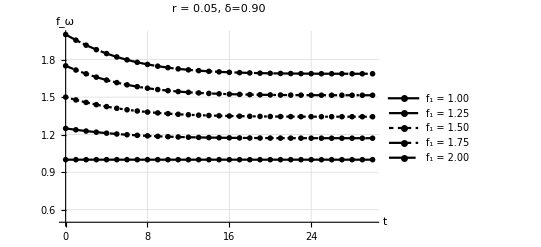

```mathematica
layers = 30
data = Table[Table[(factor -1 ) + fnew[1, factor,x,layers,0.05,0.9], {x,0,layers,1}], {factor, 1., 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 2.0}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.05, δ=0.90", PlotLegends->{"f_1 = 1.00", "f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```

{{2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.},{2.,1.97756,1.95772,1.94032,1.92515,1.91199,1.90065,1.89093,1.88262,1.87557,1.8696,1.86457,1.86035,1.85683,1.85391,1.85149,1.84949,1.84787,1.84654,1.84548,1.84462,1.84395,1.84342,1.84302,1.84271,1.84249,1.84233,1.84223,1.84216,1.84214,1.84214},{2.,1.95522,1.91502,1.87938,1.84814,1.82106,1.7978,1.778,1.76127,1.74724,1.73555,1.72586,1.71789,1.71136,1.70605,1.70175,1.69828,1.69551,1.69331,1.69158,1.69023,1.68918,1.68838,1.68778,1.68734,1.68703,1.68681,1.68667,1.68659,1.68656,1.68656},{2.,1.933,1.87191,1.81724,1.76914,1.72749,1.69191,1.6619,1.63685,1.61615,1.59918,1.58539,1.57426,1.56533,1.55822,1.55258,1.54815,1.54469,1.542,1.53993,1.53835,1.53715,1.53626,1.53561,1.53515,1.53482,1.5346,1.53446,1.53439,1.53435,1.53435},{2.,1.91089,1.82842,1.75398,1.68831,1.63158,1.58346,1.54329,1.51023,1.48334,1.46171,1.44447,1.43084,1.42014,1.4118,1.40534,1.40038,1.39658,1.3937,1.39154,1.38993,1.38874,1.38787,1.38725,1.38681,1.38651,1.38632,1.3862,1.38613,1.38611,1.38611}}

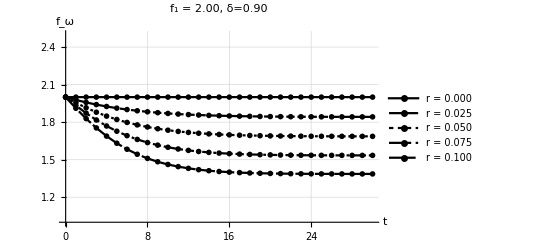

```mathematica
data = Table[Table[(1 ) + fnew[1, 2.,x,layers,rate,0.9], {x,0,layers,1}], {rate, 0., 0.1, 0.025}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.5}, AxesLabel->{"t", "f_ω"},PlotLabel-> "f_1 = 2.00, δ=0.90", PlotLegends->{"r = 0.000", "r = 0.025", "r = 0.050", "r = 0.075", "r = 0.100"}, GridLines->Automatic, DataRange->{0, layers}]
```

{{2.,1.96296,1.93578,1.91621,1.90233,1.89259,1.88581,1.88112,1.87789,1.87568,1.87417,1.87315,1.87245,1.87198,1.87166,1.87145,1.87131,1.87122,1.87116,1.87112,1.87109,1.87107,1.87106,1.87105,1.87105,1.87105,1.87105,1.87105,1.87105,1.87105,1.87105},{2.,1.9604,1.9292,1.90506,1.88664,1.87276,1.86238,1.85467,1.849,1.84483,1.84179,1.83958,1.83798,1.83682,1.83599,1.8354,1.83498,1.83468,1.83447,1.83432,1.83422,1.83415,1.8341,1.83407,1.83405,1.83404,1.83403,1.83402,1.83402,1.83402,1.83402},{2.,1.95782,1.92228,1.89281,1.8687,1.84919,1.83356,1.82114,1.81133,1.80365,1.79765,1.793,1.78941,1.78665,1.78454,1.78293,1.78171,1.78079,1.78011,1.7796,1.77922,1.77895,1.77875,1.77861,1.77852,1.77845,1.77841,1.77838,1.77837,1.77836,1.77836},{2.,1.95522,1.91502,1.87938,1.84814,1.82106,1.7978,1.778,1.76127,1.74724,1.73555,1.72586,1.71789,1.71136,1.70605,1.70175,1.69828,1.69551,1.69331,1.69158,1.69023,1.68918,1.68838,1.68778,1.68734,1.68703,1.68681,1.68667,1.68659,1.68656,1.68656},{2.,1.95262,1.90739,1.86462,1.82453,1.78728,1.75296,1.72158,1.69312,1.66751,1.64462,1.6243,1.6064,1.59073,1.5771,1.56534,1.55525,1.54667,1.53942,1.53335,1.52832,1.5242,1.52087,1.51823,1.51617,1.51461,1.51348,1.51272,1.51225,1.51204,1.51204}}

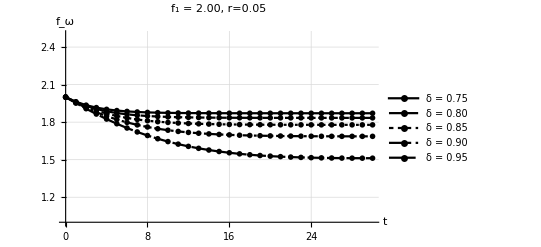

```mathematica
data = Table[Table[(1 ) + fnew[1, 2.,x,layers,0.05,delta], {x,0,layers,1}], {delta, 0.75, 0.95, 0.05}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.5}, AxesLabel->{"t", "f_ω"},PlotLabel-> "f_1 = 2.00, r=0.05", PlotLegends->{"δ = 0.75", "δ = 0.80", "δ = 0.85", "δ = 0.90", "δ = 0.95"}, GridLines->Automatic, DataRange->{0, layers}]
```

{{2.,1.95522,1.92426,1.90573,1.89759,1.89759},{2.,1.95522,1.91832,1.88889,1.86622,1.84946,1.83767,1.82997,1.82552,1.8236,1.8236},{2.,1.95522,1.91661,1.88398,1.85693,1.83493,1.81736,1.80362,1.7931,1.78526,1.77959,1.77567,1.77314,1.77169,1.77107,1.77107},{2.,1.95522,1.9158,1.88164,1.85248,1.82791,1.80749,1.79072,1.77712,1.76621,1.75757,1.75083,1.74564,1.74172,1.73883,1.73675,1.73532,1.7344,1.73388,1.73365,1.73365},{2.,1.95522,1.91533,1.88027,1.84986,1.82378,1.80166,1.78307,1.76759,1.75482,1.74436,1.73586,1.72902,1.72355,1.71922,1.71583,1.7132,1.71119,1.70968,1.70856,1.70777,1.70722,1.70687,1.70667,1.70658,1.70658},{2.,1.95522,1.91502,1.87938,1.84814,1.82106,1.7978,1.778,1.76127,1.74724,1.73555,1.72586,1.71789,1.71136,1.70605,1.70175,1.69828,1.69551,1.69331,1.69158,1.69023,1.68918,1.68838,1.68778,1.68734,1.68703,1.68681,1.68667,1.68659,1.68656,1.68656}}

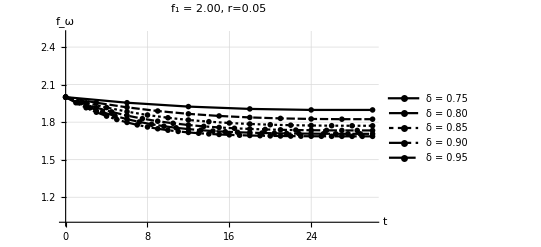

```mathematica
data = Table[Table[(1 ) + fnew[1, 2.,x,layer,0.05,0.9], {x,0,layer,1}], {layer, 5, layers, 5}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.5}, AxesLabel->{"t", "f_ω"},PlotLabel-> "f_1 = 2.00, r=0.05", PlotLegends->{"δ = 0.75", "δ = 0.80", "δ = 0.85", "δ = 0.90", "δ = 0.95"}, GridLines->Automatic]
```

```mathematica
XCLAIM
```

```mathematica
buffer = (1 + 0.1706) * (1 + 0.7634) 
f1 = 1 * buffer
```

2.06424

2.06424

12

{2.06424,2.01658,1.97639,1.94334,1.91685,1.8962,1.88057,1.86916,1.86122,1.85606,1.85309,1.85182,1.85182}

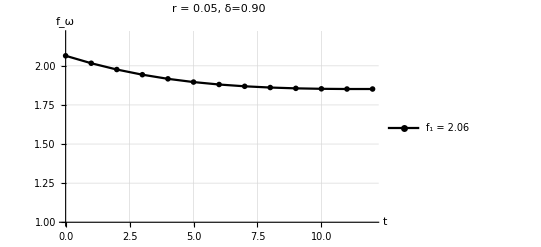

```mathematica
layers = 12
data = Table[(f1-1)+ fnew[1,f1,x,layers,0.05,0.9], {x,0,layers,1}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.2}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.05, δ=0.90", PlotLegends->{"f_1 = 2.06"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
fomega = Last[data]
```

1.85182

```mathematica
1.9797603487667936
```

```mathematica
1.9797603487667936
```

1.97976

```mathematica
1.8518166645938126
reduction = 1 - (fomega/f1)
```

1.85182

0.102905

```mathematica
Thus
```